```mathematica
ClearAll["Global`*"]
```

```mathematica
Quit[];
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Nov16/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
HFM={ dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0};
```

Energy equivalence hypothesis

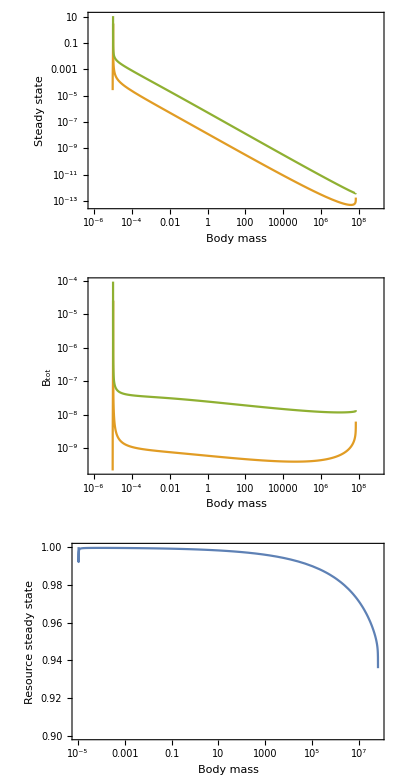

```mathematica
Cplot=GraphicsGrid[{{
LogLogPlot[{dimH/M,dimF/M},{M,.000001,10^9},Frame->True,FrameLabel->{"Body mass","Steady state"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]},{
LogLogPlot[{ HFM[[1]],HFM[[2]]},{M,.000001,10^9},Frame->True,FrameLabel->{"Body mass","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]},{
LogLinearPlot[StarRates[[1]],{M,.000001,10^9},Frame->True,PlotRange->{0.9,1},FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

```mathematica
FindMaximum[Re[HFM[[1]]],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.59227,{M→6.53794×10^7}}

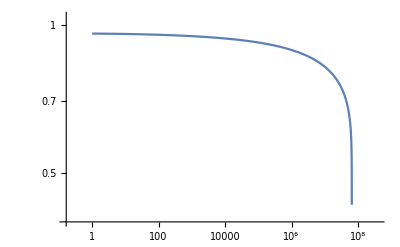

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^9},PlotRange->All]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}